```mathematica
fitkeys={age,female,asian,black,hispanic,bmi,bsa,sbp,dbp,tc,fpg,hdl,crp,tg,cursmoker,invheight,height,weight,logage};
createfitarray[basearray_,key_]:=Transpose[Join[Map[basearray,Map[ToString,fitkeys]],List[basearray[key]]]];
bar=createfitarray[riskFactor,"ITPYM"];
foo=NonlinearModelFit[bar,(a*sbp)/(b*dbp+c*weight)+d*age/height+e*sbp/height+f,{a,b,c,d,e,f},fitkeys]
quux=LinearModelFit[bar,{age,dbp,sbp,invheight,weight,logage,height},fitkeys]
foo["RSquared"]
quux["RSquared"]
Normal[foo]
Normal[quux]
```

FittedModel[-1.80668+(«1»)/(«6»)+«1»+(44.6836 «3»)/(«19» dbp+«19» «6»)]

FittedModel[-7.97902+«7»+«20» sbp-0.0121937 weight]

0.944948

0.537518

-1.80668+(2.76939 age)/height+(2.15987 sbp)/height+(44.6836 sbp)/(14.929 dbp+22.3864 weight)

-7.97902+0.0210871 age-0.0119574 dbp+0.0145154 height+1199.89 invheight-0.431677 logage+0.0278449 sbp-0.0121937 weight

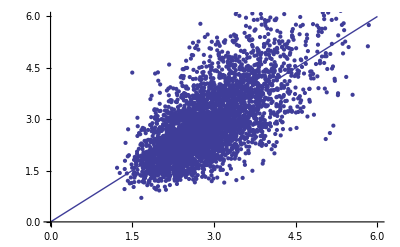

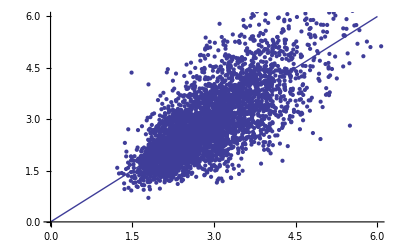

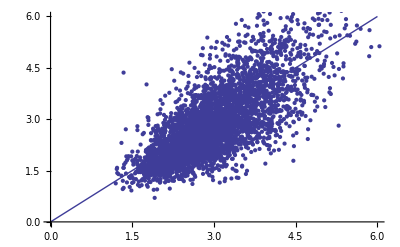

```mathematica
Show[{Plot[x,{x,0,6}],ListPlot[Transpose[{-1.38+(0.543*riskFactor["sbp"])/(0.113*riskFactor["dbp"]+0.104*riskFactor["weight"]),riskFactor["ITPYM"]}],PlotRange->{0,6},AxesOrigin->{0,0}]}]
Show[{Plot[x,{x,0,6}],ListPlot[Transpose[{-1.807+2.769*riskFactor["age"]/riskFactor["height"]+2.160*riskFactor["sbp"]/riskFactor["height"]+(44.684*riskFactor["sbp"])/(14.929*riskFactor["dbp"]+22.386*riskFactor["weight"]),riskFactor["ITPYM"]}],PlotRange->{0,6},AxesOrigin->{0,0}]}]
Show[{Plot[x,{x,0,6}],ListPlot[Transpose[{-7.979+0.021*riskFactor["age"]-0.012*riskFactor["dbp"]+0.015*riskFactor["height"]+1199.89*riskFactor["invheight"]-0.432*riskFactor["logage"]+0.028*riskFactor["sbp"]-0.012*riskFactor["weight"],riskFactor["ITPYM"]}],PlotRange->{0,6},AxesOrigin->{0,0}]}]
```